## Load Parent Notebook with Analytical Derivations

```mathematica
NotebookEvaluate["/Users/max/ellipse-double-pendulum/angular-coordinates.nb"];
```

## Choose Setup for Numerical Solution & Animation

```mathematica
(*see parent notebook for some predefined setups*)
vals=valsGeneral;
ini=iniGeneral;
tmax=50;
plotApprox=False;
```

## Solve ELEs Numerically

```mathematica
(*Geometric consideration: For Ielllipse=0 and Dspring=0, we get a singularity at this time*)
Sqrt[-b^2+a^2]/a/.vals //N
```

0.+1.73205 ⅈ

```mathematica
(*solve the exact ELEs numerically*)
sol=NDSolve[{ele1/.vals,ele2/.vals,ini[[1;;2]],ini[[3;;4]]},{th,phi},{t,0,tmax},AccuracyGoal->10]
```

{{th→InterpolatingFunction[…],phi→InterpolatingFunction[…]}}

```mathematica
(*solve the approximate ELEs numerically*)
solapprox=NDSolve[{ele1approx/.vals,ele2approx/.vals,ini[[1;;2]],ini[[3;;4]]},{th,phi},{t,0,tmax},AccuracyGoal->10]
```

{{th→InterpolatingFunction[…],phi→InterpolatingFunction[…]}}

## Animations

```mathematica
(*choose plot layout parameters*)
thisd=0.4;
thisPlotRange = Automatic;
thisPlotRange={{-thisd,+thisd},{-b-thisd,-b+thisd}}/.vals;
thisPlotRange={-Max[a,b]-thisd,+Max[a,b]+thisd}/.vals;
```

```mathematica
(*set animation type*)
animType="video"
```

video

```mathematica
(*the ellipse and point mass together*)
tmpellfunc[t_,gam_]=(r/.phi[t]->gam /. vals);
tmppttfunc[t_]=r/.vals;
ParametricPlot[{
Evaluate[tmpellfunc[#,gam]  /. sol],
If[plotApprox,Evaluate[tmpellfunc[#,gam]  /. solapprox],{}]
},
{gam,0,2Pi}, PlotRange->thisPlotRange,
Epilog->{
{Blue,PointSize@Large,Point[tmppttfunc[#]/.sol]},
If[plotApprox,{Orange,PointSize@Large,Point[tmppttfunc[#]/.solapprox]},{}]}
]&;
anim=Switch[animType,
"animation",Animate[%[t],{t,0,tmax},DefaultDuration->20.*tmax/20.],
"video",VideoGenerator[%,tmax]]
If[animType=="video",Export["/Users/max/ellipse-double-pendulum/ellipse-point-animation.mp4",anim]]
```

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

Video[/Users/max/Documents/Wolfram/Video/VideoGenerator-507bc9c8-2946-4299-9eca-77f1a2722100.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/max/Documents/Wolfram/Video/VideoGenerator-507bc9c8-2946-4299-9eca-77f1a2722100.mp4Basic1StandardForm

/Users/max/ellipse-double-pendulum/ellipse-point-animation.mp4

```mathematica
(*trajectory of the point mass*)
ParametricPlot[{
Evaluate[r /. sol /. vals],
If[plotApprox,Evaluate[r /. solapprox /. vals],None]
},
{t,-1*^-10,#},
PlotRange->thisPlotRange,
Epilog->{
{Blue,PointSize@Large,Point[r /. sol /. vals /. t->#]},
If[plotApprox,{Orange,PointSize@Large,Point[r /. solapprox /. vals /. t->#]},{}]
}
]&;
anim=Switch[animType,
"animation",Animate[%[T],{T,0,tmax},DefaultDuration->20.*tmax/20.],
"video",VideoGenerator[%,tmax]]
If[animType=="video",Export["/Users/max/ellipse-double-pendulum/point-animation.mp4",anim]]
```

Video[/Users/max/Documents/Wolfram/Video/VideoGenerator-74766579-7567-4ddd-abcf-f7388e027069.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/max/Documents/Wolfram/Video/VideoGenerator-74766579-7567-4ddd-abcf-f7388e027069.mp4Basic1StandardForm

/Users/max/ellipse-double-pendulum/point-animation.mp4

```mathematica
(*trajectory of the ellipse*)
ParametricPlot[{
Evaluate[{a Sin[th[t]],-b Cos[th[t]]} /. sol /. vals],
If[plotApprox,{a Sin[th[t]],-b Cos[th[t]]} /. solapprox /. vals,None]
},
{t,-1*^-10,#},
PlotRange->thisPlotRange,
Epilog->{
{Blue,PointSize@Large,Point[{a Sin[th[#]],-b Cos[th[#]]}/.sol/.vals]},
If[plotApprox,{Orange,PointSize@Large,Point[{a Sin[th[#]],-b Cos[th[#]]}/.sol/.vals]},{}]
}
]&;
anim=Switch[animType,
"animation",Animate[%[T],{T,0,tmax},DefaultDuration->20.*tmax/20.],
"video",VideoGenerator[%,tmax]]
If[animType=="video",Export["/Users/max/ellipse-double-pendulum/ellipse-animation.mp4",anim]]
```

Video[/Users/max/Documents/Wolfram/Video/VideoGenerator-14f40ede-c20b-456d-9b12-3373bbbcb98b.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/max/Documents/Wolfram/Video/VideoGenerator-14f40ede-c20b-456d-9b12-3373bbbcb98b.mp4Basic1StandardForm

/Users/max/ellipse-double-pendulum/ellipse-animation.mp4

## Trajectories

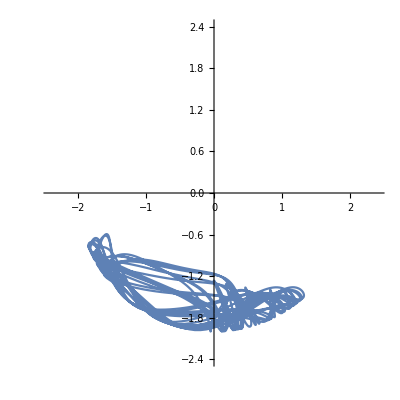

```mathematica
(*point mass*)
ParametricPlot[{
Evaluate[r /. sol /. vals],
If[plotApprox,Evaluate[r /. solapprox /. vals],None]
},{t,0,tmax}, PlotRange->thisPlotRange]
```

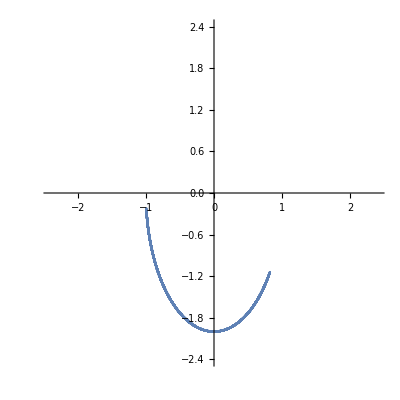

```mathematica
(*elliptical wire*)
ParametricPlot[{
Evaluate[{a Sin[th[t]],-b Cos[th[t]]}/. sol /. vals],
If[plotApprox,Evaluate[{a Sin[th[t]],-b Cos[th[t]]}/. solapprox/. vals],None]
},{t,0,tmax}, PlotRange->thisPlotRange]
```

## Plots

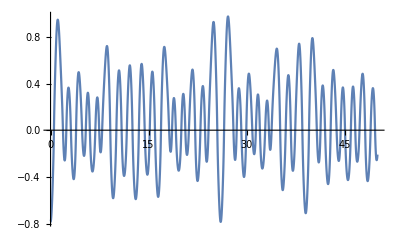

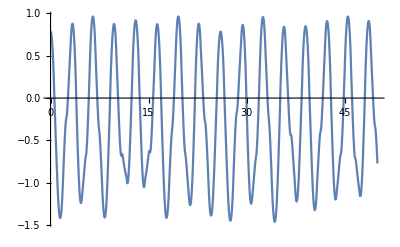

```mathematica
Plot[{
Evaluate[phi[t]/. sol],
If[plotApprox,Evaluate[phi[t]/. solapprox],None]
},{t,0,tmax},PlotRange->All]
Plot[{
Evaluate[th[t]/. sol],
If[plotApprox,Evaluate[th[t]/. solapprox],None]
},{t,0,tmax},PlotRange->All]
```

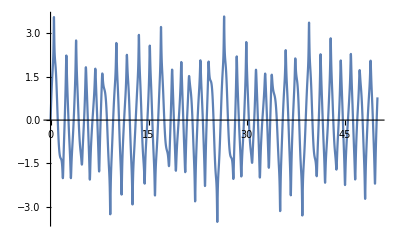

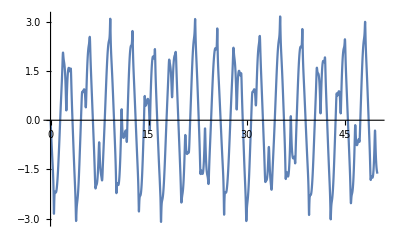

```mathematica
Plot[{
Evaluate[phi'[t]/. sol],
If[plotApprox,Evaluate[phi'[t]/. solapprox],None]
},{t,0,tmax},PlotRange->All]
Plot[{
Evaluate[th'[t]/. sol],
If[plotApprox,Evaluate[th'[t]/. solapprox],None]
},{t,0,tmax},PlotRange->All]
```

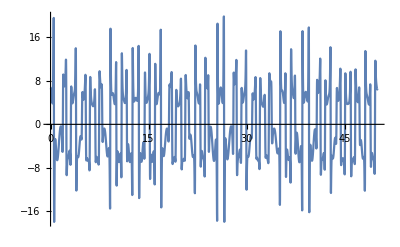

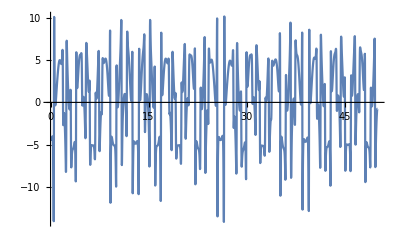

```mathematica
Plot[{
Evaluate[phi''[t]/. sol],
If[plotApprox,Evaluate[phi''[t]/. solapprox],None]
},{t,0,tmax},PlotRange->All]
Plot[{
Evaluate[th''[t]/. sol],
If[plotApprox,Evaluate[th''[t]/. solapprox],None]
},{t,0,tmax},PlotRange->All]
```

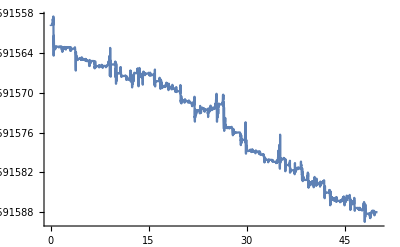

```mathematica
(*energy over time*)
Plot[{
Evaluate[Ttot+Vtot /.vals/. sol],
If[plotApprox,Evaluate[Ttot+Vtot /. vals/. solapprox],None]
},{t,0,tmax},PlotRange->All]
```